(-2-√3 x0-x1) (-2+√3 x0+x1)

(-2+√3 x0-x1) (-2-√3 x0+x1)

-1+x1^2

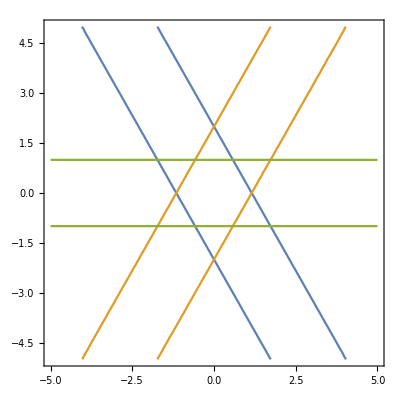

-3 x0^2-2 √3 x0 x1-x1^2+4 x2^2

-3 x0^2+2 √3 x0 x1-x1^2+4 x2^2

x1^2 - x2^2

```mathematica
f1 = (√3 x0 + x1 - 2)(-√3 x0 - x1  - 2)
f2 = (-√3 x0 + x1  - 2)(√3 x0 - x1  - 2)
f3 = (x1^2 - 1)
ContourPlot[{f1 == 0, f2 ==0, f3 == 0} ,{x0,-5,5},{x1,-5,5}]

h1 = ResourceFunction["PolynomialHomogenize"][Expand[f1],{x0, x1},x2]
h2 = ResourceFunction["PolynomialHomogenize"][Expand[f2],{x0, x1},x2]
h3 = ResourceFunction["PolynomialHomogenize"][Expand[f3],{x0, x1},x2];
h1 //InputForm
h2 //InputForm
h3 //InputForm
```

```mathematica
d = -3*x0^2+2*a*x0*x1-x1^2+4*x2^2,x1^2-x2^2;
s = d /. u2-> 1
ContourPlot[s == 0, {u0, -5, 5}, {u1, -5, 5}]
```